```mathematica
a=1;b=3;n=20;
```

```mathematica
h=(b-a)/n//N;
m=n/2
```

10

```mathematica
f[x_]=E^(-x^2/2);
```

```mathematica
prib=h/3*(f[a]+2*Sum[f[a+2*i*h],{i,1,m-1}]+4*Sum[f[a+(2*i-1)*h],{i,1,m}]+f[b])
```

0.394305

```mathematica
cetvrti[x_]=D[f[x],{x,4}]
```

3 ⅇ^(-x^2/2)-6 ⅇ^(-x^2/2) x^2+ⅇ^(-x^2/2) x^4

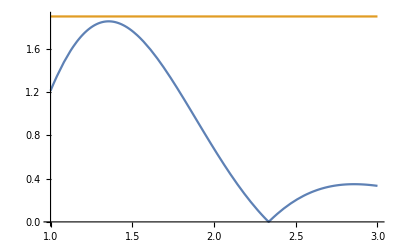

```mathematica
Plot[{Abs[cetvrti[x]],1.9},{x,1,3}]
```

```mathematica
m4=1.9;
```

```mathematica
greska=(b-a)/180*m4*h^4
```

2.11111×10^-6

```mathematica
njutn[f_,x_,x0_,eps_]:=Module[{},
iter[0]=x0//N;
izvod=D[f,x];
i=0;
While[Abs[(f/.x->iter[i])]>=eps,
iter[i+1]=iter[i]-(f/.x->iter[i])/(izvod/.x->iter[i]);
i=i+1;
];
iter[i]
]
```

```mathematica
f[x_]=2 x^5+5 x^2-17;x0=1;eps=10^-4;
```

```mathematica
njutn[f[x],x,x0,eps]
```

1.32622

```mathematica
a=({{25, -1, 2, -1}, {0, 20, 3, 1}, {-1, -1, 20, 3}, {1, 1, -2, 22}});b=({{2}, {1}, {-1}, {0}});x0=({{1}, {-1}, {1}, {1}});
```

```mathematica
jakobi[a_,b_,x0_,kmax_]:=Module[{},
res={x0};
itnew=x0//N;
n=Length[x0];
Do[
itold=itnew;
Do[
itnew[[i,1]]=-1/a[[i,i]](Sum[a[[i,j]]*itold[[j,1]],{j,1,i-1}]+Sum[a[[i,j]]*itold[[j,1]],{j,i+1,n}]-b[[i,1]]),
{i,1,n}];
res=Append[res,itnew],
{k,1,kmax}];
res
]
```

```mathematica
jakobi[a,b,x0,10]
```

{{{1},{-1},{1},{1}},{{0.},{-0.15},{-0.2},{0.0909091}},{{0.0936364},{0.0754545},{-0.0711364},{-0.0113636}},{{0.0882545},{0.0612386},{-0.0398409},{-0.0141529}},{{0.0850707},{0.0566838},{-0.0404024},{-0.010417}},{{0.0850829},{0.0565812},{-0.0413497},{-0.0101163}},{{0.0851666},{0.0567083},{-0.0413993},{-0.0101983}},{{0.0851723},{0.0567198},{-0.0413765},{-0.0102124}},{{0.0851704},{0.0567171},{-0.0413735},{-0.0102111}},{{0.0851701},{0.0567166},{-0.041374},{-0.0102107}},{{0.0851702},{0.0567166},{-0.0413741},{-0.0102107}}}

```mathematica
ok[f_,t_,y_,a_,b_,y0_,n_]:=Module[{},
ttac[0]=a;
wit[0]=y0;
h=(b-a)/n//N;
Do[
ttac[i+1]=ttac[i]+h;
wit[i+1]=wit[i]+h*f/.{t->ttac[i],y->wit[i]},
{i,0,n-1}];
Table[{ttac[k],wit[k]},{k,0,n}]
]
```

```mathematica
f[t_,y_]=y+5Cos[t]
```

y+5 Cos[t]

```mathematica
ok[f[t,y],t,y,0,2,2,20]
```

{{0,2},{0.1,2.7},{0.2,3.4675},{0.3,4.30429},{0.4,5.21238},{0.5,6.19415},{0.6,7.25236},{0.7,8.39026},{0.8,9.61171},{0.9,10.9212},{1.,12.3242},{1.1,13.8267},{1.2,15.4362},{1.3,17.161},{1.4,19.0108},{1.5,20.9969},{1.6,23.132},{1.7,25.4306},{1.8,27.9092},{1.9,30.5865},{2.,33.4835}}